```mathematica
(*
Run this functions

*)



(*

This is an auxiliar function to find the position of each point inside a list of points.
*)
findpos=Block[{test,test1,test2,tru1,tru2,i,j,tabx,taby},

tabx=#3;
taby=#4;
i=1;
j=1;
test=False;
test1=False;
test2=False;
tru1=False;
tru2=False;

While[test==False,

If[test1==False,
If[tabx[[i]]≤ #1[[1]]≤ tabx[[i+1]],

test1=True;

If[

(*
If[
Abs[tabx[[i+1]]]≤ 10^-12,
2*tabx[[i]]-#2*Abs[tabx[[i]]],tabx[[i+1]]-#2*Abs[tabx[[i+1]]]]

≤ #1[[1]]
*)
tabx[[i+1]]-#2*Abs[(tabx[[i+1]]-tabx[[i]])]≤ #1[[1]]
,tru1=True;];

,
i=i+1;
];

If[i==Length[tabx]-1,
test1=True;
];
];


If[test2==False,

If[taby[[j]]≤ #1[[2]]≤ taby[[j+1]],

test2=True;
If[

(*
If[
Abs[taby[[j+1]]]≤ 10^-12,

2*(taby[[j]])-#2*Abs[taby[[j]]],taby[[j+1]]-#2*Abs[taby[[j+1]]]

]≤ #1[[2]]

*)
taby[[j+1]]-#2*Abs[(taby[[j+1]]-taby[[j]])]≤ #1[[2]]


,tru2=True;];
,
j=j+1;
];

If[j==Length[taby]-1,
test2=True;
];

];


If[(test1==True)&&(test2==True),
test=True
];



];

{{i,j},{tru1,tru2}}
]&;



(*
This is the main function ;

Variables:;

#1: data points as a list {{x1,y1,χ^2(x1,y1)},...}      ;
  #2: one degree of freedom confidence level, ie: σ      ;

The Optional parameters are:;

"NumberStepsx": Number of grid steps in the x direction. Defaut 4;
"NumberStepsx": Number of grid steps in the y direction. Defaut equal to x.;
"IntersectionSize": how close to the previous part of the slash of the figure it will start (in percent). Defaut 0.1 ;
"Color": The color of the final plot. Defaut Opacity[0.5,Lighter[Blue];
"Details"; Show plot. Defaut 0;

Output: Graphic object with the full union region of all the parts from the data selected;


*)

Options[region]={"NumberStepsx"-> 4,"NumberStepsy"-> 0,"IntersectionSize"-> 0.1,"Color"->Opacity[0.5,Lighter[Blue]] ,"Details"->0};
region[points_,σ_,OptionsPattern[]]:=Block[{aux,b,array1,k,hulls,data,dataux,xi,xf,yi,yf,nnx,nny,tabx,taby,test1,test2,counter},



nnx=OptionValue["NumberStepsx"];

If[OptionValue["NumberStepsy"]≤ 0,

nny=nnx;,
nny=OptionValue["NumberStepsy"];

];

data=points;
dataux={};

(*

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
Select all the point in the data with χ^2< #2^2 ;
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
*)
Do[
If[data[[i,3]]≤ σ^2,
dataux=Append[dataux,{data[[i,1]],data[[i,2]]}];

];

,{i,1,Length[data]}];

(*Create the grid to collect the points in the data*)
data=dataux;

dataux=Table[data[[i,1]],{i,1,Length[data]}];
xi=Min[dataux];
xf=Max[dataux];


dataux=Table[data[[i,2]],{i,1,Length[data]}];
yi=Min[dataux];
yf=Max[dataux];



tabx=Table[xi+(xf-xi)*(i-1)/nnx,{i,1,nnx+1}];
taby=Table[yi+(yf-yi)*(i-1)/nny,{i,1,nny+1}];

array1=Table[{},{i,1,Length[tabx]-1},{j,1,Length[taby]-1}];


(*
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
     Colect the data points in the right part;
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
*)

Do[



aux=findpos[{data[[i,1]],data[[i,2]]},OptionValue["IntersectionSize"],tabx,taby];


array1[[aux[[1,1]],aux[[1,2]]]]=Append[array1[[aux[[1,1]],aux[[1,2]]]],{data[[i,1]],data[[i,2]]}];


If[(aux[[2,1]]==True)&&(aux[[1,1]]<Length[array1]),


aux[[1,1]]=aux[[1,1]]+1;

];

If[(aux[[2,2]]==True)&&(aux[[1,2]]<Length[array1[[1]]]),

aux[[1,2]]=aux[[1,2]]+1;

];

If[((aux[[2,2]]==True)&&(aux[[1,2]]≤  Length[array1[[1]]]))||((aux[[2,1]]==True)&&(aux[[1,1]]≤  Length[array1])),

array1[[aux[[1,1]],aux[[1,2]]]]=Append[array1[[aux[[1,1]],aux[[1,2]]]],{data[[i,1]],data[[i,2]]}];
];


,{i,1,Length[data]}];


(*
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
     Create the convex Hulls from the points;
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%;
*)


array1=Flatten[array1,1];
k=0;
Do[

If[Length[array1[[k2]]]<3, (*This ensures that we have at least 3 points in the array (enough to creat a region *)
(*do nothing*)
,(*else*)
test1=0;
counter=2;




(*This test is to ensure that the points are not in a line so it has an area*)
While[test1==0&&counter≤ Length[array1[[k2]]],

If[
array1[[k2]][[1,1]]≠ array1[[k2]][[counter,1]],
(*else*)
test1=1;

];

counter=counter+1;

];

test2=0;
counter=2;

While[test2==0&&counter≤ Length[array1[[k2]]],

If[
array1[[k2]][[1,2]]≠ array1[[k2]][[counter,2]],
(*else*)
test2=1;
];

counter=counter+1;

];

If[(test1==1)&&(test2==1),
k=k+1;
b[k]=ConvexHullMesh[array1[[k2]]];
];

]


,{k2,1,Length[array1]}];

If[k==0,
Print["No points Found"];
,
(*
Show[Table[b[i],{i,1,k}],Frame->True,PlotRange-> All,AspectRatio-> 1]
*)
hulls=Table[b[k1],{k1,1,k}];
If[OptionValue["Details"]==0,
Show[{
Graphics[Show[Pick[hulls,RegionDimension/@hulls,2]//RegionUnion]/.{Directive[x_]:>Directive[{OptionValue["Color"],EdgeForm[{OptionValue["Color"],Thickness[0.001]}]}]}]
},AspectRatio-> 0.5,PlotRange->All,Frame-> True],

Show[{
Graphics[Show[Pick[hulls,RegionDimension/@hulls,2]//RegionUnion]/.{Directive[x_]:>Directive[{OptionValue["Color"],EdgeForm[{OptionValue["Color"],Thickness[0.001]}]}]}]
,ListPlot[data,PlotStyle->Darker[ OptionValue["Color"]]]},AspectRatio-> 0.5,PlotRange->All,Frame-> True]

]
]

]


Print["Loaded"];
```

Loaded

```mathematica
SetDirectory[NotebookDirectory[]];

data=Import["mixing3_chisq_dcp_0_dune_hist.dat","Table"];

data=Table[{data[[i,1]],data[[i,2]], 11.83},{i,1,Length[data]}];
```

```mathematica
{"NumberStepsx"-> 4,"NumberStepsy"-> 0,"IntersectionSize"-> 0.1,"Color"->Opacity[0.5,Lighter[Blue]] ,"Details"->0};
```

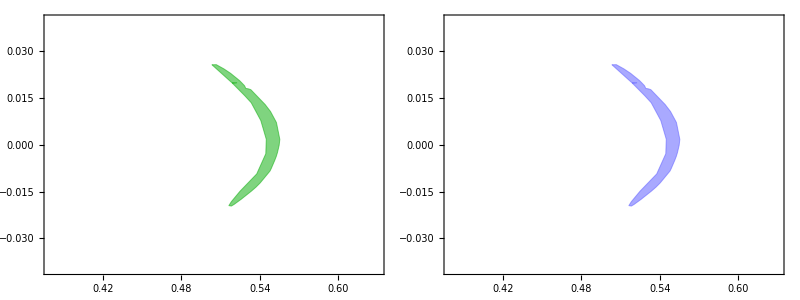

```mathematica
Grid[{{Show[{region[data,4,"NumberStepsx"-> 2,"NumberStepsy"-> 8,"Details"->0,"IntersectionSize"-> 0.3,"Color"->Opacity[0.5,Darker[Green]]]},PlotRange-> {{.38,.63},{-.04,.04}},ImageSize-> 700],Show[{region[data,4,"NumberStepsx"-> 2,"NumberStepsy"-> 8,"Details"->0,"IntersectionSize"-> 0.3]},PlotRange-> {{.38,.63},{-.04,.04}},ImageSize-> 700]}}]
```